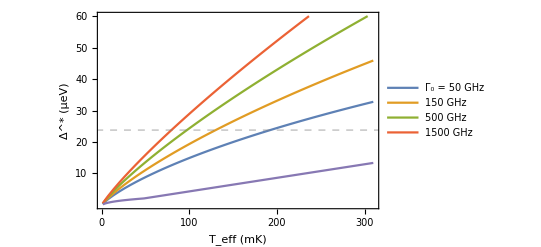

```mathematica
GHzToMicroeV=4.13567;
GHzToMilliK=48.0;

ClearAll[myDelta,mykT,myGamma0]

eq[mykT_?NumericQ,myDelta_,myGamma0_?NumericQ]:=Piecewise[{{2 myDelta/mykT-Log[myGamma0/mykT]==mykT/(2 myDelta),mykT<myGamma0},{2 myDelta/mykT==mykT/(2 myDelta),mykT>=myGamma0}}]

deltaSol[mykT_?NumericQ,myGamma0_?NumericQ]:=myDelta/. FindRoot[eq[mykT,myDelta,myGamma0],{myDelta,1}]

deltaPhysical[TmK_?NumericQ,gamma0GHz_?NumericQ]:=Module[{kTGHz,deltaGHz},(*convert input temperature->GHz*)kTGHz=TmK/GHzToMilliK;
(*solve equation*)deltaGHz=deltaSol[kTGHz,gamma0GHz];
(*convert output->micro eV*)GHzToMicroeV*deltaGHz]

Plot[Evaluate@Table[deltaPhysical[T,g0],{g0,{50,150,500,1500,1}}],
{T,1,310},(*temperature in mK*)
Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"T_eff (mK)","Δ^* (μeV)",None,None},
PlotRange->{{1,310},{0,60}},
FrameTicks->{{{10,20,30,40,50,60},None},{{0,100,200,300},None}},
PlotLegends->{"Γ_0 = 50 GHz","150 GHz","500 GHz","1500 GHz"},
GridLines->{None,{23.8}},
GridLinesStyle->Directive[Thick,Gray,Dashed]
]
```